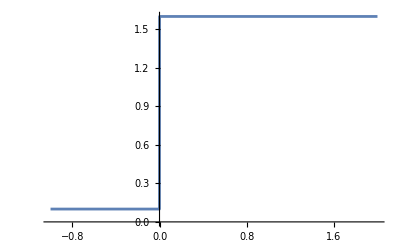

{{v→InterpolatingFunction[…]}}

```mathematica
Clear["Global`*"]
Vin[t_]:=1.5 HeavisideTheta[2 t]+0.1
Plot[Vin[t],{t,-1,2}]
r = 100;
c = 10^(-3);
τ = r *c;
eqn = v'[t] * τ + v[t]==Vin[t];
Vo = NDSolve[{eqn,v[1]==0},v,{t,0,2 }]
```

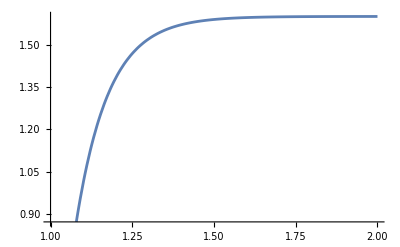

```mathematica
Plot[Evaluate[v[t] /. Vo],{t,1,2}]
```

Piecewise[{{(-1+t)^2, t<1}, {Log[t], t≥1}, {0, True}}]

{{v→InterpolatingFunction[…]}}

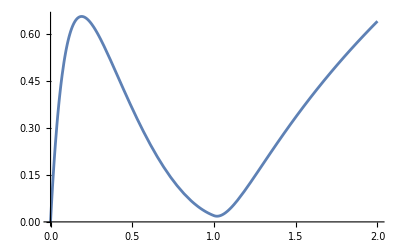

```mathematica
Clear["Global`*"]
Vin[t_] = Piecewise[{{(t-1)^2,t<1} , {Log[t],t>=1}}]
eqn = v'[t] * 0.1 + v[t]==Vin[t]; /. τ -> 0.1
Vo = NDSolve[{eqn,v[0]==0},v,{t,0,2,0.1 }]
Plot[Evaluate[v[t] /. Vo],{t,0,2}]
```

Piecewise[{{0.6 SquareWave[t], t<0.003}, {0, True}}]

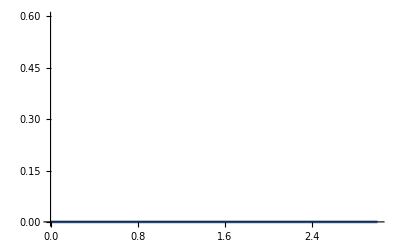

{{v→InterpolatingFunction[…]}}

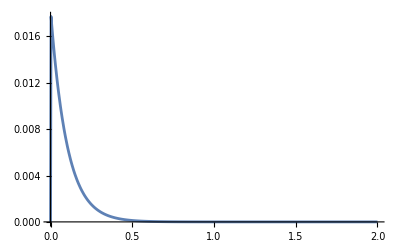

```mathematica
Clear["Global`*"]
Vin[t_] = Piecewise[{{0.6 *SquareWave[t], t<0.003}, {0, t>0.003}}]
Plot[Vin[t], {t,0,3}]
eqn = v'[t] * 0.1 + v[t]==Vin[t]; 
Vo = NDSolve[{eqn,v[0]==0},v,{t,0,2,0.001 }]
Plot[Evaluate[v[t] /. Vo],{t,0,2}, PlotRange->All]
```

1/(1+(ⅈ ω)/10)

1/(1+ω^2/100)

-ω/(10 (1+ω^2/100))

ArcTan[ω/10]

√(1/((1+ω^2/100)^2)+ω^2/(100 (1+ω^2/100)^2))

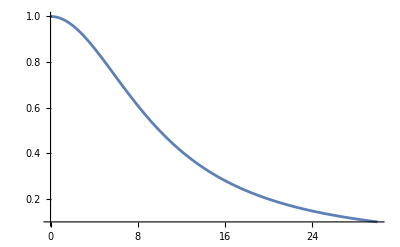

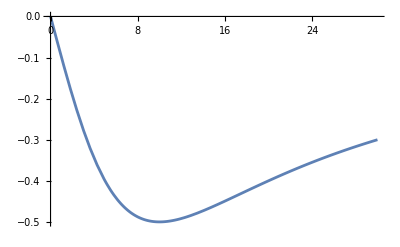

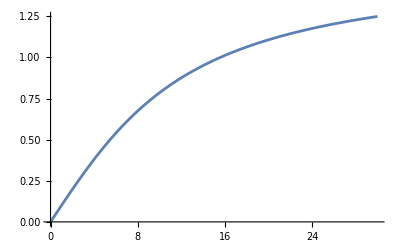

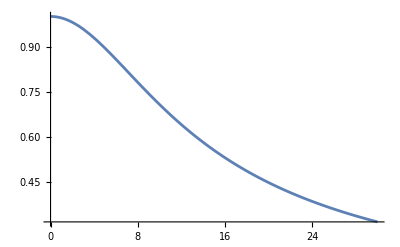

```mathematica
r = 100;
c = 10^(-3);
H[ω_] = 1/(1+ I ω r c)
RealH[ω_] = 1/(1+(ω r c )^2)
ImH[ω_] =- ω r c /(1+(ω r c )^2)
phase[ω_] =  -ArcTan[ ImH[ω]/RealH[ω]]
Len[ω_] = Sqrt[ImH[ω]^2 + RealH[ω]^2]
Plot[RealH[ω] , {ω,0,30}, PlotRange->All]
Plot[ImH[ω] , {ω,0,30}]
Plot[phase[ω] , {ω, 0,30}]
Plot[Len[ω] , {ω,0,30}]
```

## Part 4

Piecewise[{{0.6 SquareWave[t], t<0.003}, {0, True}}]

-Graphics-

{{v→InterpolatingFunction[…]}}

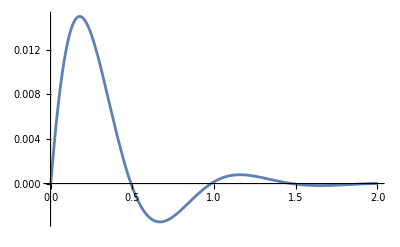

0.6 SquareWave[t]

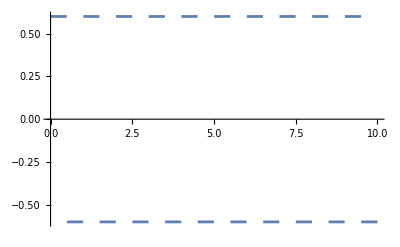

50 b[t]+6 b'[t]+b''[t]==60. SquareWave[t]

{{b→InterpolatingFunction[…]}}

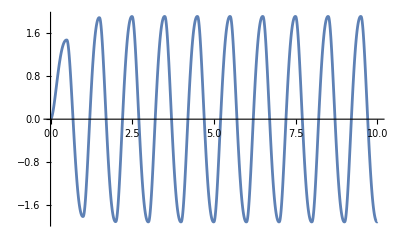

```mathematica
Clear["Global`*"]

Vin[t_] = Piecewise[{{0.6 *SquareWave[t], t<0.003}, {0, t>0.003}}]
Plot[Vin[t], {t,0,3}]
eqn = v''[t] + 6v'[t] + 50v[t] == 100 Vin[t]; 
Vo = NDSolve[{eqn,v[0]==0, v'[0] == 0},v,{t,0,2,0.001 }]
Plot[Evaluate[v[t] /. Vo],{t,0,2}, PlotRange->All]


Vin2[t_] = 0.6 SquareWave[t] 
Plot[Vin2[t], {t,0,10}]
eqn2 = b''[t] + 6b'[t] + 50b[t] == 100 Vin2[t]
Vo2 = NDSolve[{eqn2,b[0]==0,b'[0] == 0},b,{t,0,10,0.1 }]
Plot[Evaluate[b[t] /. Vo2],{t,0,10}]
```

Piecewise[{{(-1+t)^2, 0<t<1}, {Log[t], t≥1}, {0, True}}]

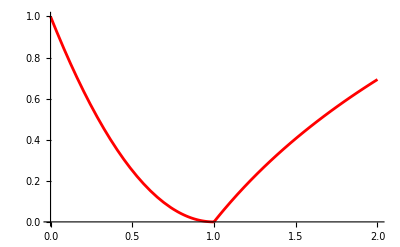

{{v→InterpolatingFunction[…]}}

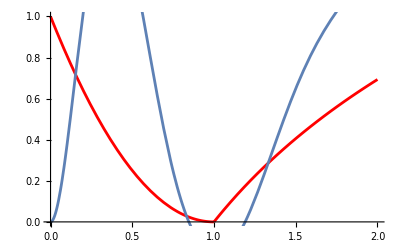

```mathematica
Clear["Global`*"]
Vin[t_] = Piecewise[{{(t-1)^2,0<t<1  } , {Log[t],t>=1}}]
pltin = Plot[Vin[t],{t,0,2}, PlotStyle->Red]
eqn = v''[t] + 6v'[t] + 50v[t] == 100 Vin[t]; 
Vo = NDSolve[{eqn,v[0]==0, v'[0] == 0},v,{t,0,2,0.001 }]
plto = Plot[Evaluate[v[t] /. Vo],{t,0,2}, PlotRange->All];
Show[{pltin, plto}]
```